```mathematica
s=NDSolve[{y'[x]+{-0.0001{y[x]}^2+2y[x]}/(2x) -5==0,y[10]==10},y,{x,10,5}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[y[x]/.s],{x,10,5}]
```

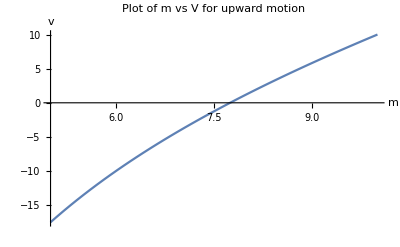

```mathematica
Show[%113,AxesLabel->{HoldForm[m],HoldForm[v]},PlotLabel->HoldForm[Plot of m vs V for upward motion],LabelStyle->{GrayLevel[0]}]
```

```mathematica
s=NDSolve[{{100-2t}y'[t]+2y[t]==-10(100-2t)-0.0001{y[t]}^2,y[0]==50},y,{t,0,30}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[y[t]/.s],{t,0,30}]
```

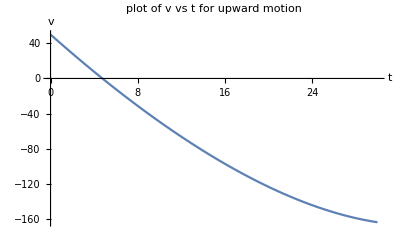

```mathematica
Show[%162,AxesLabel->{HoldForm[t],HoldForm[v]},PlotLabel->HoldForm[plot of v vs t for upward motion],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Plot[10Tanh[0.1(t-5)],{t,5,50}]
```

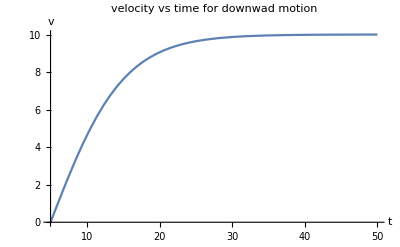

```mathematica
Show[%170,AxesLabel->{HoldForm[t],HoldForm[v]},PlotLabel->HoldForm[velocity vs time for downwad motion],LabelStyle->{GrayLevel[0]}]
```